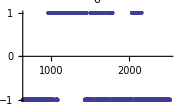
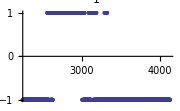
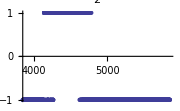
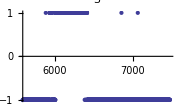
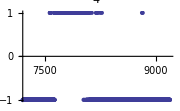
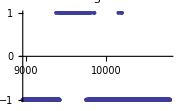
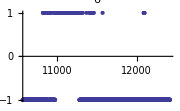
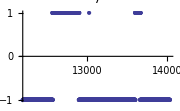

```mathematica
Table[(
data = Import["/home/mhh/predictions/logisticRegression2/Proband1/SM/laplacian/test"<>ToString[i]<>"Predictions"];
ListPlot[ MovingAverage[data,1], ImageSize-> Small, PlotLabel->ToString[i]]
),{i,0,9}]
```